```mathematica
(*Author: Mohamed Kamal AbdElrahman
Date Apr 24, 2022
 
Regression with Neural Networks in Wolfram Langauge

Goals:
	1- what neural newtworks are ?  Layers ? Functions ? Compositions ?
 2- linear regression with linear layers  
  3- why we need nonlinearity ?
 4- why we need to  go to higher dimensions ? 
*)
```

## Linear/Nonlinear Regression with Neural Nets

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mk/Desktop/DeepLearningWithMathematica/Linear Regression

```mathematica
FileNames[]
```

{RegressionNN.nb,test.csv,train.csv}

```mathematica
trainSet = Import["train.csv"];
testSet = Import["test.csv"];
```

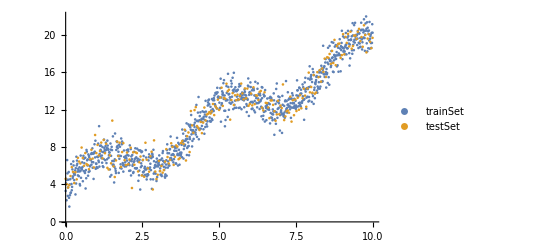

```mathematica
ListPlot[{trainSet,testSet},PlotLegends->{"trainSet","testSet"}]
```

### Linear Regression

```mathematica
f = NetInitialize[LinearLayer[{},"Input"->{}]]
```

LinearLayer[<>]

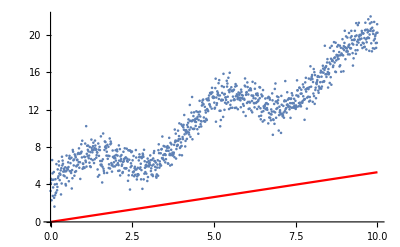

```mathematica
Show[ListPlot[trainSet],Plot[f[x],{x,0,10},PlotStyle->Red]]
```

```mathematica
trainedf = NetTrain[f,trainSet[[All,1]]->trainSet[[All,2]],TimeGoal->10]
```

LinearLayer[<>]

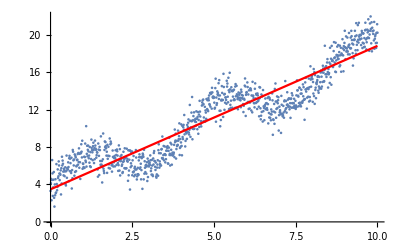

```mathematica
Show[ListPlot[trainSet],Plot[trainedf[x],{x,0,10},PlotStyle->Red]]
```

```mathematica
NetMeasurements[trainedNet,testSet[[All,1]]->testSet[[All,2]],"MeanSquare"]
```

3.20441

## Adding more Linear Layers

```mathematica
f11 = NetInitialize[NetChain[{{},{},{}},"Input"->{}]]
```

NetChain[<>]

```mathematica
trainedf11 = NetTrain[f11,trainSet[[All,1]]->trainSet[[All,2]],TimeGoal->10]
```

NetChain[<>]

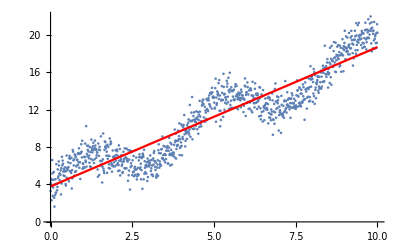

```mathematica
Show[ListPlot[trainSet],Plot[trainedf11[x],{x,0,10},PlotStyle->Red]]
```

## Adding a Nonlinearity

```mathematica
f2 = NetInitialize[NetChain[{{},LogisticSigmoid,{}},"Input"->{}]]
```

NetChain[<>]

```mathematica
trainedf2 = NetTrain[f2,trainSet[[All,1]]->trainSet[[All,2]],TimeGoal->40]
```

NetChain[<>]

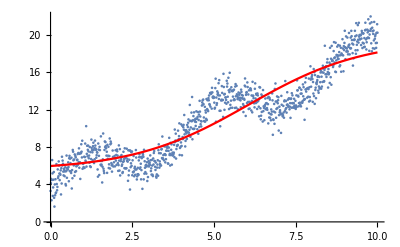

```mathematica
Show[ListPlot[trainSet],Plot[trainedf2[x],{x,0,10},PlotStyle->Red]]
```

## Adding More Nonlinearity

```mathematica
f3 = NetInitialize[NetChain[{{},Tanh,{},Tanh,{},Tanh,{},Tanh,{}},"Input"->{}]]
```

NetChain[<>]

```mathematica
trainedf3 = NetTrain[f3,trainSet[[All,1]]->trainSet[[All,2]],TimeGoal->40]
```

NetChain[<>]

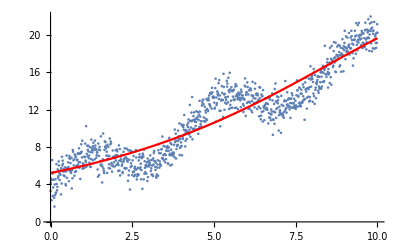

```mathematica
Show[ListPlot[trainSet],Plot[trainedf3[x],{x,0,10},PlotStyle->Red]]
```

## Going to Higher Dimensions

```mathematica
f4 = NetInitialize[NetChain[{{10},Tanh,{}},"Input"->{}]]
```

NetChain[<>]

```mathematica
trainedf4 = NetTrain[f4,trainSet[[All,1]]->trainSet[[All,2]],TimeGoal->40]
```

NetChain[<>]

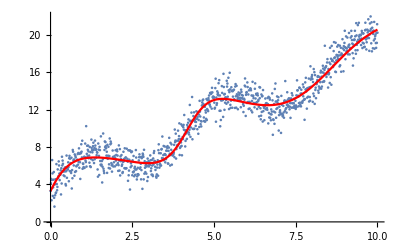

```mathematica
Show[ListPlot[trainSet],Plot[trainedf4[x],{x,0,10},PlotStyle->Red]]
```